# II Distributions

KTH/EECS:IX1501 - Mathematical Statistics
HT 2019

## Section. Implementation and Assessment

The course includes three mandatory project tasks on a total of 3.5 hp.  They will be given a summary grade in Pass/Fail (G/U).

In project 1 and 2,  you will work in a group of two and solve a mathematical task, write a report (English) in Mathematica and prepare a short oral presentation on your solution to the task (English).

Carefully read the following information so that you know which rules apply and what is expected from you.

### Section.Subsection Report

The report should be written in Mathematica and contain

title and authors of the report

email@kth.se

a summary containing the results of resolved parts

separate sections for each part containing e.g.

mathematical formulas and equations

a brief discussion

explanatory diagrams

your conclusions.

separate code section (do not mix code and text with conclusions and results)

The report must be uploaded a day before the examination (see 1.4 below).

### Section.Subsection Oral Presentation

You should prepare an oral presentation of your solution to the task. The presentation will be carried out with your own laptop and should not take more than five minutes, effective time. A projector will be available at the presentation. Please carefully consider your presentation, what is important, in what order and how it will be illustrated. Practice the presentation in advance and make sure to meet the time frame. One of you in the group (of two) will be selected randomly for the oral presentation and the other will be selected for questioning.

### Section.Subsection Rules

The task is considered individually and assumes that you have full knowledge of all the material you are presenting. In order to be approved, then you must have solved the task and be able to explain the entire task and solution.

To account for the task that you do not have solved is considered cheating. It is also cheating to copy the whole or a part of a solution from others. If two solutions are deemed as (partial) copies, both will be rejected.

If the solution contains parts that you do not have produced, e.g. background material, you must clearly indicate this and specify the source.

Suspicion of cheating or misbehaving can be reported to the Disciplinary Board.

### Section.Subsection Examination

The examination is carried out according to the booking in Canvas.

The booking is done according to the information in Canvas  Projektuppgifter/Projekt 2.

Please note that this project should be reported in group of two students.

The report (including code section) should be uploaded before deadline according to the information in Canvas  Projektuppgifter/Projekt 2.

A printed copy of the report must be submitted at the examination. Don’t print the code section.

Notice that the report shall always be uploaded in time even if you cannot attend at the oral presentation. In case of illness, etc., then the oral presentation may be made during reserved timeslots. If you are unable to attend, you must in advance inform the teachers, Sara Khosravi (sarakhos@kth.se) and Ki Won Sung (sungkw@kth.se), by email.

If you ignore the oral presentation or the uploading of the report without contacting the teachers (in writing), you will have to wait for the next course for a new project exam.

## Section. Preparations

### Section.Subsection Study

Read and study the following texts:

Chapters 6, 7, 8

lecture notes F7-F10

### Section.Subsection Guidance

#### Section.Subsection.Subsubsection Language Tip

In Mathematica 11, by default, you get automatic spell-checking in English. When a word is marked as misspelled, e.g. atomatic. You can right-click the word and get a what-to-do menu. Use the second syntax above to inactivate spell-checking.. 

If you want to use Swedish in a future, this can be a bit annoying. To set the language to Swedish or to turn off the spell-checking, execute one of the following commands in your notebook. Then, delete the code and save your notebook.

SetOptions[EvaluationNotebook[], DefaultNaturalLanguage -> "Swedish"]

SetOptions[EvaluationNotebook[], ShowAutoSpellCheck -> False]

#### Section.Subsection.Subsubsection Using estimated cdf

##### Section.Subsection.Subsubsection.Subsubsubsection Using the inverse function

If you want to check your data against a presumed model you can visually see that you’re on the right track by applying the inverse model function to your data.

We will give an example where the model, a simple 2^nd degree polynomial, is known. We start by generating data from the polynomial with some random error.

```mathematica
ClearAll["`*"]
```

```mathematica
model[x_]:=0.1(x+1)^2+2
```

```mathematica
err:=RandomReal[{-1,1}];
```

```mathematica
data=Table[{x,model[x+err]},{x,0,50}]
```

{{0,2.05764},{1,2.47612},{2,2.54901},{3,4.13438},{4,5.22389},{5,6.89898},{6,6.8015},{7,9.26722},{8,11.0439},{9,11.303},{10,13.3014},{11,16.1507},{12,20.4694},{13,22.4635},{14,26.0971},{15,29.0625},{16,33.6464},{17,32.0163},{18,41.1942},{19,42.5062},{20,42.2578},{21,46.3626},{22,53.8177},{23,58.5883},{24,64.0226},{25,68.4234},{26,76.372},{27,84.7277},{28,90.8663},{29,88.2884},{30,98.1574},{31,98.2619},{32,104.734},{33,122.176},{34,118.201},{35,137.657},{36,141.998},{37,144.038},{38,161.21},{39,167.336},{40,170.942},{41,184.151},{42,185.993},{43,192.151},{44,210.378},{45,205.527},{46,224.057},{47,237.239},{48,246.958},{49,243.228},{50,265.923}}

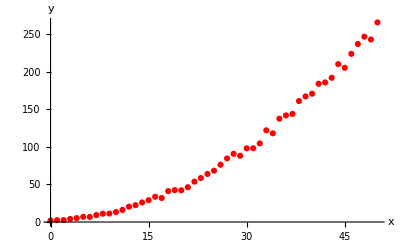

```mathematica
dataPlot=ListPlot[data,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Red]
```

Now let’s say we want to test the model y=a x^2+b x+c. We can see that y is increasing if x is increasing and y>b≈2. Solving for x we get (taking the + root).

y=a x^2+b x+c⇔y=a (x+b/(2 a))^2-b^2/(4 a)+c⇒x=1/(√c)√y+a-b/(√c)⇔√y=√c(x-a)+b

So if our model is correct we would get a straight line if we take the square root of the y-data.

```mathematica
invfun[y_]:=√y;
invfun[{x_,y_}]:={x,√y}
```

```mathematica
idata=invfun/@data
```

{{0,1.43445},{1,1.57357},{2,1.59656},{3,2.03332},{4,2.28558},{5,2.62659},{6,2.60797},{7,3.04421},{8,3.32324},{9,3.36199},{10,3.6471},{11,4.01879},{12,4.52431},{13,4.73956},{14,5.10853},{15,5.39097},{16,5.80055},{17,5.65829},{18,6.41827},{19,6.51968},{20,6.5006},{21,6.80901},{22,7.33606},{23,7.6543},{24,8.00141},{25,8.27184},{26,8.73911},{27,9.20477},{28,9.53238},{29,9.39619},{30,9.90744},{31,9.91272},{32,10.234},{33,11.0533},{34,10.872},{35,11.7327},{36,11.9163},{37,12.0016},{38,12.6968},{39,12.9358},{40,13.0745},{41,13.5702},{42,13.6379},{43,13.8619},{44,14.5044},{45,14.3362},{46,14.9685},{47,15.4026},{48,15.7149},{49,15.5958},{50,16.3072}}

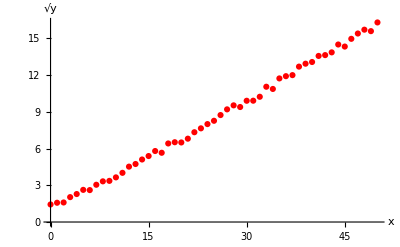

```mathematica
idataPlot=ListPlot[idata,AxesLabel->{HoldForm[x],HoldForm[√y]},PlotStyle->Red]
```

If we had the correct inverse function we would get the identity line y=x. In this case with √y we get a straight line, but with a slope that’s not 1 and with a y-intercept that’s not 0.

```mathematica
Clear[α,β];
{α,β}={α,β}/.FindFit[idata,α x+β,{α,β},x]
```

{0.303962,0.859689}

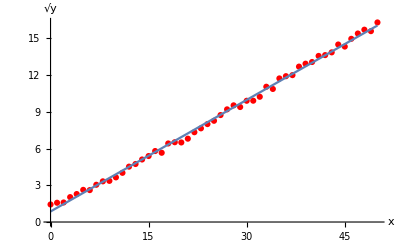

```mathematica
iplot=Plot[α x+β,{x,0,50}];
Show[idataPlot,iplot]
```

We have a model y(x)=(α x+β)^2

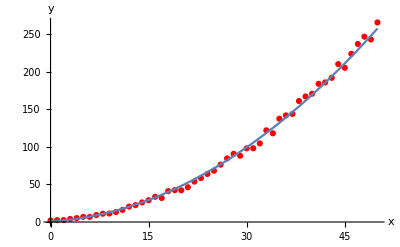

```mathematica
mplot=Plot[(α x+β)^2,{x,0,50}];
Show[dataPlot,mplot]
```

Now, let’s say we choose another (erroneous) model, y=e^(a x+b). How does it look like?

y=e^(a x+b)⇔ln(y)=a x+b

```mathematica
invModel2[v_]:=Log[y];
invModel2[{x_,y_}]:={x,Log[y]}
```

```mathematica
idata2=invModel2/@data
```

{{0,0.721559},{1,0.906694},{2,0.935704},{3,1.41934},{4,1.65324},{5,1.93137},{6,1.91714},{7,2.22648},{8,2.40188},{9,2.42507},{10,2.58787},{11,2.78196},{12,3.01893},{13,3.11189},{14,3.26182},{15,3.36945},{16,3.51591},{17,3.46624},{18,3.7183},{19,3.74965},{20,3.74379},{21,3.83649},{22,3.9856},{23,4.07054},{24,4.15924},{25,4.22571},{26,4.33562},{27,4.43944},{28,4.50939},{29,4.48061},{30,4.58657},{31,4.58764},{32,4.65142},{33,4.80546},{34,4.77239},{35,4.92476},{36,4.95581},{37,4.97007},{38,5.08271},{39,5.12},{40,5.14133},{41,5.21576},{42,5.22571},{43,5.25828},{44,5.3489},{45,5.32558},{46,5.4119},{47,5.46907},{48,5.50922},{49,5.494},{50,5.58321}}

```mathematica
Clear[α,β];
{α,β}={α,β}/.FindFit[idata2,α x+β,{α,β},x]
```

{0.0889028,1.66658}

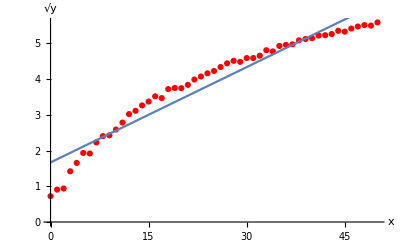

```mathematica
idataPlot2=ListPlot[idata2,AxesLabel->{HoldForm[x],HoldForm[√y]},PlotStyle->Red];
iplot2=Plot[α x+β,{x,0,50}];
Show[idataPlot2,iplot2]
```

We can see that a straight line doesn’t fit these data so the model, y=e^(α x+β) is not good.

##### Section.Subsection.Subsubsection.Subsubsubsection General ideas

If your model is an exponential function, then the log(y)-lin(x) plot will give you a straight line.

y=c e^(k x)⇔ln(y)=ln(c)+k x⇔ln(y)=k x+m⇔y=e^(k x+m)

In a LogPlot or ListLogPlot the base 10 is used:

y=c 10^(k x)⇔log_10(y)=log_10(c)+k x⇔log_10(y)=k x+m⇔y=10^(k x+m)

Example

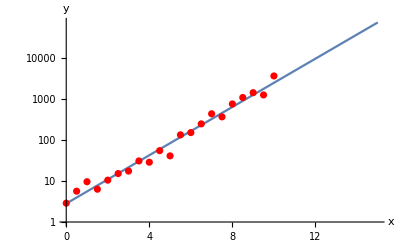

We can see that our model can be used for prediction, for example y(15).

The other way around: assume that our model e^(a y+b)=x is the right one.

ⅇ^(a y+b)=x⇔a y+b=ln(x)⇔y=1/a ln(x)-b/a⇔y=k ln(x)+m

In other words, if we compute the logarithm of x-data we get a straight line so a lin(y)-log(x) plot will give you a straight line. This is accomplished in a LogLinearPlot or ListLogLinearPlot.

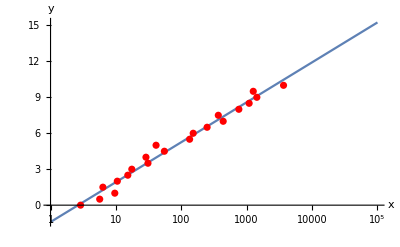

Finally, assume our model is y=c x^k, i.e. a power function.

y=c x^k⇔ln(y)=ln(c)+k ln(x)⇔ln(y)=k ln(x)+m⇔y=e^m x^k

That is, if data compute the logarithm for both x and y we get a straight line so a log(y)-log(x) plot will give you a straight line. This is accomplished in a LogLogPlot or ListLogLogPlot.

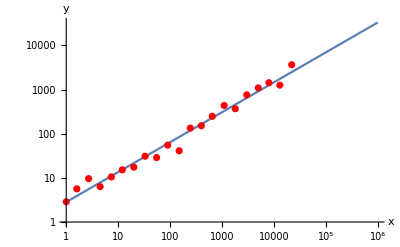

##### Section.Subsection.Subsubsection.Subsubsubsection An estimated cdf

Assume you have a sample from some (unknown) random variable.

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
?randomExample
```

```mathematica
ClearAll["`*"]
```

```mathematica
n=1000;
𝕩=randomExample[n];
Short[𝕩]
```

Now, you want to view the distribution of these data. We can see that the data probably is from a continuous distribution. Usually the pdf is not a good idea since it expresses density rather than probability. Further it’s difficult to differentiate numerical data. So our choice is to go for the cdf.

cdf(t)=P(X≤x)

This means that we want to translate the sample 𝕩 into probabilities. For a certain value this can be done by simply counting how many values that are ≤x_i. An easy way to do this counting is to sort all values.

```mathematica
𝕩sort=Sort[𝕩];
```

One approach here is to set let each value correspond to and increase of Δ=1/n probability. It’s also reasonable to let each value correspond to the mid point in the Δ-interval so the first value x_1 corresponds to P(X≤x_1)=Δ/2 and the value x_k to P(X≤x_k)=Δ/2+(k-1) Δ.

```mathematica
Δ=1/n;
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
Short[𝕡data]
```

```mathematica
𝕩𝕡data=Transpose[{𝕩sort,𝕡data}];
```

Now, a plot of our estimated cdf is

```mathematica
ListPlot[𝕩𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}]
```

There is a built-in method for this, namely the Quantile.

```mathematica
qdata=Table[{Quantile[𝕩,q],q},{q,0,1,0.01}];
ListLinePlot[qdata,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}]
```

We will use these data values again in the upcoming section.

##### Section.Subsection.Subsubsection.Subsubsubsection Comparing the cdf

We have seen how the inverse function can be used to verify a model y=f(x) by comparing x_data and x_model=f(y_data). In principle we compare two x-axes to each other.

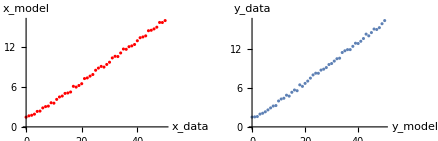

Another approach is simply to use the model function directly. Then, we don’t have to worry about inverse function. This means that we are comparing y-axes instead.This is particularly useful in the cdf case since the output (or y-values) is always in the interval [0,1].

We are now going to compare the previous data to a presumed model. Let’s use the data of Section  Section.Subsection.Subsubsection.Subsubsubsection. We start the examination by computing estimates of the expectation value and the standard deviation. In the upcoming lectures you will learn how to estimate these. However, here we use the built-in estimates Mean and StandardDeviation (which are the same).

x̄=1/n∑_(i=1)^n x_i, s=√(1/(n-1)∑_(i=1)^n (x_i-x̄)^2)

```mathematica
x=Mean[𝕩]
```

```mathematica
s=StandardDeviation[𝕩]
```

Now we want to check the data against the normal cdf. In order to do that we have to compute the normal cdf values from our data.

```mathematica
𝒩=NormalDistribution[x,s]
```

```mathematica
𝕡model=CDF[𝒩,𝕩sort];
```

```mathematica
comparedata=Transpose[{𝕡model,𝕡data}];
```

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```

We can see that the alignment is not so good. Let’s try another model, gamma distribution (I know that this is right, since I’m the designer here). We have to estimate the parameters (α,β) from our data.

```mathematica
Clear[α,β];
𝒢=EstimatedDistribution[𝕩,GammaDistribution[α,β]]
```

Now, we’ve got the distribution so we can compare it with our model.

```mathematica
𝕡model=CDF[𝒢,𝕩sort];
```

```mathematica
comparedata=Transpose[{𝕡model,𝕡data}];
```

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Gamma distribution",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```

We can see that this is a good line fit so we accept the model. There are also numerical methods to compare the model with data, e.g. χ^2-test (see DistributionFitTest).

##### Section.Subsection.Subsubsection.Subsubsubsection A distribution example with built-in methods

In Mathematica there are many powerful built-in methods for statistical investigations. We can match the data directly to different distributions.

Let’s use the data of Section  Section.Subsection.Subsubsection.Subsubsubsection. and first have a look at our normal distribution approach which wasn’t any good.

```mathematica
𝒩=EstimatedDistribution[𝕩,NormalDistribution[μ,σ]]
```

EstimatedDistribution::insffdt: There is insufficient data to proceed with the computation. The data must contain at least 1 elements.

EstimatedDistribution[𝕩,NormalDistribution[μ,σ]]

```mathematica
ProbabilityPlot[𝕩,𝒩]
```

We can see that this is not a good line fit so we don’t accept the model. Let’s try another one:

```mathematica
𝒢=EstimatedDistribution[𝕩,GammaDistribution[α,β]]
```

```mathematica
ProbabilityPlot[𝕩,𝒢]
```

We get a clear indication that gamma distribution is the better choice. Notice that the comparison is dependent on the sample size. If the sample is too small the comparison might be ambiguous.

You could use your own model also, using ProbabilityDistribution. Assume that we have the following model for the pdf(x):

pdf(x)∝x^2 e^(-a x), x>0

The constant of proportion c is determined by

```mathematica
Clear[a,c,x,𝒟];
i=Integrate[x^2 ⅇ^(-a x),{x,0,∞},Assumptions->{a>0}]
```

2/a^3

```mathematica
c=1/i
```

a^3/2

The pdf(x) is then

```mathematica
pdf[x_]=c x^2 ⅇ^(-a x)
```

1/2 a^3 ⅇ^(-a x) x^2

Our distribution is introduced by

```mathematica
𝒟[a_]=ProbabilityDistribution[pdf[x],{x,0,∞},Assumptions->{a>0}]
```

ProbabilityDistribution[1/2 x^2 a^3 ⅇ^(-x a),{x,0,∞},Assumptions→{a>0}]

```mathematica
myDist=EstimatedDistribution[𝕩,𝒟[a]]
```

EstimatedDistribution::insffdt: There is insufficient data to proceed with the computation. The data must contain at least 1 elements.

EstimatedDistribution[𝕩,ProbabilityDistribution[1/2 x^2 a^3 ⅇ^(-x a),{x,0,∞},Assumptions→{a>0}]]

```mathematica
ProbabilityPlot[𝕩,myDist]
```

Since this is close to the Γ-distribution we get a really good fit.

#### Section.Subsection.Subsubsection Confidence interval

##### Section.Subsection.Subsubsection.Subsubsubsection Theory

Let’s say we want to estimate μ from samples of normal distribution X_i∈N(μ,σ) with known σ. Our point estimate will be the arithmetic mean

X^—=1/n∑_(i=1)^n X_i

Since we assume that the sample consists of independent observations X_i we can use the simple addition property of the normal distribution.

E(X^—)=1/n∑_(i=1)^n μ=μ, V(X^—)=1/n^2∑_(i=1)^n σ^2=σ^2/n⇒X^—∈N(μ,σ/(√n))⇒(X^—-μ)/(σ/√n)∈N(0,1)

Now if we want a symmetric interval [X̄-x_ℓ,X̄+x_ℓ] to cover μ with probability c (confidence level). How can we compute the limits ±x_ℓ? We want the probability that X̄ is outside the interval to be 1-c. Half of this should be on the right side.

P(X^—>μ+x_ℓ)=(1-c)/2⇔P(X^—≤μ+x_ℓ)=1-(1-c)/2⇔P(X^—≤μ+x_ℓ)=(1+c)/2

⇔Φ(((μ+x_ℓ)-μ)/(σ/√n))=(1+c)/2⇔Φ(x_ℓ/(σ/√n))=(1+c)/2⇔x_ℓ/(σ/√n)=q_N((1+c)/2)⇔x_ℓ=q_N((1+c)/2)σ/(√n)

where q_N is the quantile for N(0,1). In the practical situation we have a data sample {x_i}_(i=1)^n instead of stochastic variables {X_i}_(i=1)^n so we can write the confidence interval as

ci_μ=x^—±q_N((1+c)/2)σ/(√n)

See NormalDistribution and Quantile.

Now let’s say we don’t know σ. Our point estimate will then be

S=√(1/(n-1)∑_(i=1)^n (X_i-X^—)^2)⇒(X^—-μ)/(S/√n)∈𝔱(n-1)

The estimate now depends on both X̄ and S so the situation is more complicated. It has been shown that the distribution for the point estimate is the student’s t-distribution with f=n-1 degrees of freedom (see StudentTDistribution). We will not go deeply into this so we just accept the fact and use the t-distribution which has the following pdf.

pdf_𝔱(x)=((1+x^2/f)^(-(f+1)/2))/(√f f/21/2)

lim_(f→∞) pdf_𝔱(x)=φ(x)

where ab=a b/a+b is the Beta function. As f→∞ we approach the normal distribution.

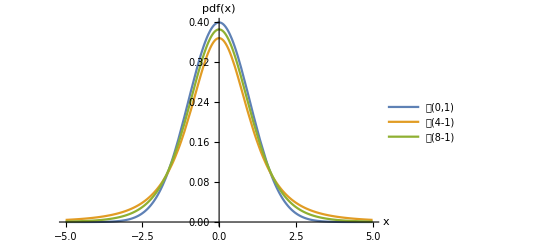

The pdf_𝔱(x) is wider the than φ(x) which gives a larger quantile in the confidence interval which is given by

ci_c=x^—±q_𝔱(n-1,(1+c)/2)s/(√n)

x̄=1/n∑_(i=1)^n x_i, s=√(1/(n-1)∑_(i=1)^n (x_i-x^—)^2)

Notice that when X_i∈𝒩(μ,σ) with known or unknown σ the given confidence intervals are exact (even when the sample size is low).

##### Section.Subsection.Subsubsection.Subsubsubsection CLT

According to the Central Limit Theorem the estimate

X^—=1/n∑_(i=1)^n X_i

will approach normal distribution if the sample size is “large enough”. The needed size is dependent on the distribution of X_i. If X_i have a symmetric distribution and iid (independent identical distributed) it’s often enough with a sample size of 20.

It has been shown that the CLT is useful under more general conditions (for a large sample). The X_i-distributions can be different and X_i can also be weakly dependent.

When using CLT, the approximate 𝔱 confidence interval is

ci_μ≈x̄±q_𝔱(n-1,(1+c)/2)s/(√n)

if σ is estimated by s. If σ is known or can be derived directly from x̄ use the approximate 𝒩 confidence interval

ci_μ≈x̄±q_𝒩((1+c)/2)σ/(√n)

This is the situation when X_i∈exp(λ) since μ=σ=1/λ. Notice that when X_i∉𝒩(μ,σ) the given confidence intervals are approximate and that you have to ensure large enough sample size.

In hand calculation you often ignore the difference between 𝔱- and 𝒩-distribution and if the sample size is large enough (e.g. 100).

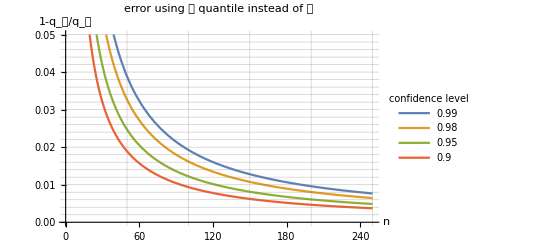

Notice that when X_i∉𝒩(μ,σ) the given confidence intervals are approximate and that you have to ensure large enough sample size.

##### Section.Subsection.Subsubsection.Subsubsubsection Example with manual calculation

We will now continue with the example from section  Section.Subsection.Subsubsection.Subsubsubsection, but we increase the sample size and compute a 95% confidence interval for μ is according to section Section.Subsection.Subsubsection.Subsubsubsection.

```mathematica
q=Quantile[StudentTDistribution[n-1],0.975]
```

```mathematica
x=Mean[𝕩]
```

```mathematica
s=StandardDeviation[𝕩]
```

```mathematica
n
```

```mathematica
ciμ = {x - q*(s/Sqrt[n]), x + q*(s/Sqrt[n])}
```

```mathematica
cilen=ciμ⟦2⟧-ciμ⟦1⟧
```

Notice that the length (or width) of the interval is inversely proportional to √n. If we use the same q and s, we can calculate a new sample size n_new based on a desired length ℓ_new.

ℓ=2(q s)/(√n)⇒ℓ_new/ℓ=(1/√n_new)/(1/√n)⇒n_new=n (ℓ/ℓ_new)^2

Notice that you have to add some margin here, since if you use the calculate n you have roughly 50% probability that the interval will be too long. Now, let’s say we want a confidence interval that’s shorter than 0.1.

```mathematica
margin=2;
nnew=Ceiling[margin*n*(cilen/0.1)^2]
```

```mathematica
𝕩=randomExample[nnew];
```

```mathematica
x=Mean[𝕩]
```

```mathematica
s=StandardDeviation[𝕩]
```

```mathematica
ciμ = {x - q*(s/Sqrt[nnew]), x + q*(s/Sqrt[nnew])}
```

There is still a risk that the interval is too short. In that case give it another try, adding more samples.

##### Section.Subsection.Subsubsection.Subsubsubsection Using built-in methods

Confidence intervals like the ones in previous section can be found by loading Hypothesis Testing Package. The confidence intervals for μ and σ^2 using CLT can then be found by simple method calls. Example:

```mathematica
data=randomExample[50]
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
(* confidence interval for μ *)
MeanCI[data, ConfidenceLevel->0.95]
```

```mathematica
(* confidence interval for σ^2 *)
VarianceCI[data,ConfidenceLevel->0.95]
```

```mathematica
(* confidence interval for σ *)
√VarianceCI[data,ConfidenceLevel->0.95]
```

Now, we want to find confidence intervals for the parameters α and β for our chosen distribution model. We will use a direct method here, using EstimatedDistribution to get {α,β} pairs and then apply CLT. This means that we will create data according to section  Section.Subsection.Subsubsection.Subsubsubsection. We will also continue the approach in section  Section.Subsection.Subsubsection.Subsubsubsection.

We can get estimate of the parameters of our chosen model by

```mathematica
Clear[α,β];m=100;
𝒟=EstimatedDistribution[randomExample[m],GammaDistribution[α,β]]
```

Applying List will give us the desired α,β pair.

```mathematica
List@@𝒟
```

The idea now is to repeat this enough times so that the CLT gives us good confidence intervals.

```mathematica
n=50;
𝕩=randomExample[{n,m}];
```

```mathematica
findαβ[data_]:=List@@EstimatedDistribution[data,GammaDistribution[α,β]]
```

```mathematica
{𝕒,𝕓}=Transpose[findαβ/@𝕩]
```

```mathematica
ciα=MeanCI[𝕒, ConfidenceLevel->0.95]
```

```mathematica
ciβ=MeanCI[𝕓, ConfidenceLevel->0.95]
```

## Section. Mathematical Task

Keep in mind that it is the mathematical method on the task that is interesting to consider, not a simple answer. Furthermore, solve the given task, not a variant or extension.

Read Section 2.2 Guidance very carefully before delving into the mathematical tasks!

A general hint is to start in a small scale and test your methods with not too large numbers.

It is better to take advantage of that you are using a mathematical programming language. You don’t need to “re-invent the wheel”.

### Which distribution?

Together with this notebook there is a package file Project2.m with a random number generator from secret distributions. Put the package file in the same directory as this notebook. You load the package (once a session) with the following code:

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

You can then use the method randomNumber[i, n] to generate n random numbers from distribution i. For example,

```mathematica
?randomNumber
```

```mathematica
randomNumber[6,100]
```

{17,7,7,8,9,5,8,13,7,13,5,6,13,12,10,9,13,10,10,10,8,12,7,10,7,10,8,8,10,14,12,12,10,11,12,11,12,10,7,6,7,6,9,7,9,13,15,8,11,9,7,10,10,8,9,4,12,14,6,6,4,11,16,11,6,9,13,13,10,10,6,10,10,6,6,9,18,8,16,11,11,9,15,6,8,15,5,7,7,6,9,7,9,15,8,6,18,13,9,10}

In this task, randomNumber[i, n] can be used to generate data for the distributions i=1,2,…,6. They are all distributions that are mentioned in the course literature (Blom Sec. 3.4 and Sec. 3.6). Do the following assignments for each of six distributions, i.e. i∈{1,2,…,6}.

Use the straight line approach to determine a distribution model.

Determine point estimates of the parameters.

Compute 95% confidence intervals for the parameters. The interval should not be longer than 10% of its mean, e.g. μ (1±0.05).

```mathematica
n = 1000;
a1 = randomNumber[1,n];
a2 = randomNumber[2,n];
a3 = randomNumber[3,n];
a4 = randomNumber[4,n];
a5 = randomNumber[5,n];
a6 = randomNumber[6,n];
a1sorted = Sort[a1];
a2sorted = Sort[a2];
a3sorted = Sort[a3];
a4sorted = Sort[a4];
a5sorted = Sort[a5];
a6sorted = Sort[a6];
```

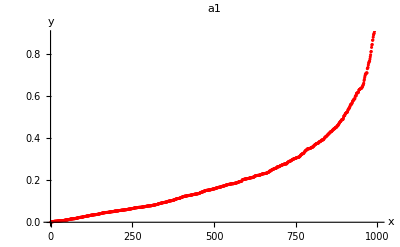

```mathematica
ListPlot[a1sorted, AxesLabel -> {HoldForm[x], HoldForm[y]}, PlotStyle-> Red, PlotLabel ->"a1"]
```

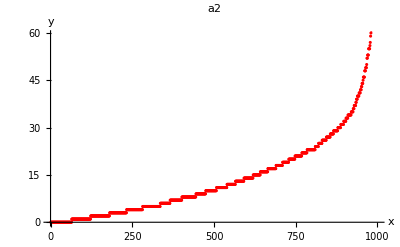

```mathematica
ListPlot[a2sorted, AxesLabel -> {HoldForm[x], HoldForm[y]}, PlotStyle-> Red, PlotLabel ->"a2"]
```

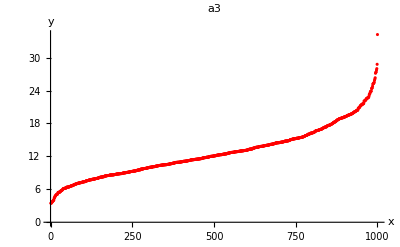

```mathematica
ListPlot[a3sorted, AxesLabel -> {HoldForm[x], HoldForm[y]}, PlotStyle-> Red, PlotLabel ->"a3"]
```

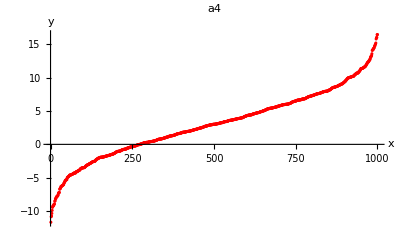

```mathematica
ListPlot[a4sorted, AxesLabel -> {HoldForm[x], HoldForm[y]}, PlotStyle-> Red, PlotLabel ->"a4"]
```

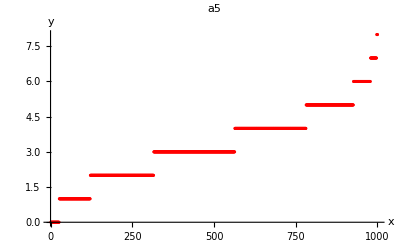

```mathematica
ListPlot[a5sorted, AxesLabel -> {HoldForm[x], HoldForm[y]}, PlotStyle-> Red, PlotLabel ->"a5"]
```

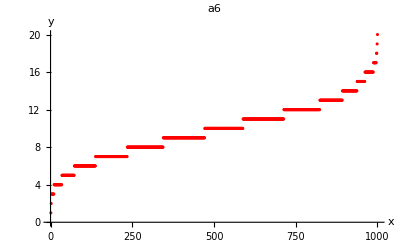

```mathematica
ListPlot[a6sorted, AxesLabel -> {HoldForm[x], HoldForm[y]}, PlotStyle-> Red, PlotLabel ->"a6"]
```

```mathematica
Δ=1/n;
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
```

Range::range: Range specification in Range[0,1-1/n,1/n] does not have appropriate bounds.

Range::range: Range specification in Range[0.,1.-1./n,1/n] does not have appropriate bounds.